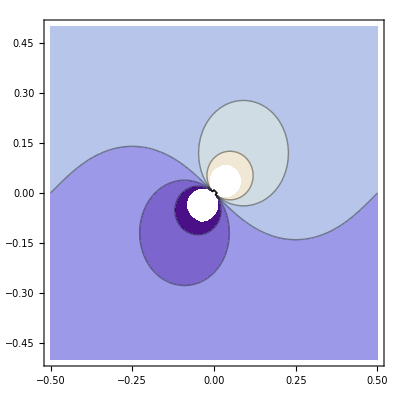

```mathematica
(* Cycle potential on a cylinder *)
ContourPlot[Re[(1+I)/π Cot[(x+I y)π]],{x,-1/2,1/2},{y,-1/2,1/2}]
```

```mathematica
(* Real expression *)
(I (Exp[2 I (x + I y)] + 1)/(Exp[2 I (x+I y)] - 1)-I (Exp[-2 I (x - I y)] + 1)/(Exp[-2 I (x-I y)] - 1))/2//FullSimplify
```

-Sin[2 x]/(Cos[2 x]-Cosh[2 y])

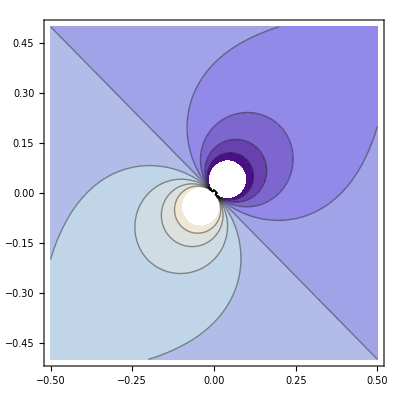

```mathematica
(* cycle potential on a torus *)
ContourPlot[Re[(1+I)WeierstrassPPrime[x + I y,WeierstrassInvariants[{1,I}]]/WeierstrassP[x+I y,WeierstrassInvariants[{1,I}]]],{x,-1/2,1/2},{y,-1/2,1/2}]
```